### Trajectories of weak-field orbital evolution via gravitational radiation reaction in Schwarzschild - de Sitter spacetime

In this notebook we show the plots of orbital trajectories for compact objects around Schwarzschild black holes influenced by an SdS parameter λ (y in this notebook). Results of this notebook has been used in Villanueva, John Adrian N., and Ian Vega. “Extreme-mass ratio inspirals in Schwarzschild-de Sitter spacetime I: Weak-field orbits.” arXiv preprint arXiv:2602.17154 (2026). https://arxiv.org/abs/2602.17154

We solve for the system of osculating orbital parameters,

-Graphics-

### Orbital equations:

```mathematica
fdot[p_,e_,f_,y_]:=(√(1/p^3)-y/(2 √(1/p^3)))(1+e Cos[f])^2
deldot[p_,e_,f_,y_]:=(√(1/p^3)-y/(2 √(1/p^3)))3/p
pdot[p_,e_,y_]:=-(8 (1-e^2)^(3/2) (8+7 e^2))/(5 p^3)+(16 (-1+e^2)+(4 (-168-283 e^2+26 e^4))/(15 (1-e^2)^(3/2))) y
edot[p_,e_,y_]:=-(e (1-e^2)^(3/2) (304+121 e^2))/(15 p^4)+((2 (-24-965 e^2-784 e^4+73 e^6))/(15 e (1-e^2)^(3/2) p)+(32 (1-e^2)^(3/2) (-1+√(1-e^2)))/(3 e p)) y
```

### Solvers

2.5pN, λ = 0

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.7,p[0]==50,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-7],e'[t]==edot[p[t],e[t],10^-7],f'[t]==fdot[p[t],e[t],f[t],10^-7],δ'[t]==deldot[p[t],e[t],f[t],10^-7],f[0]==0,e[0]==0.7,p[0]==50,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

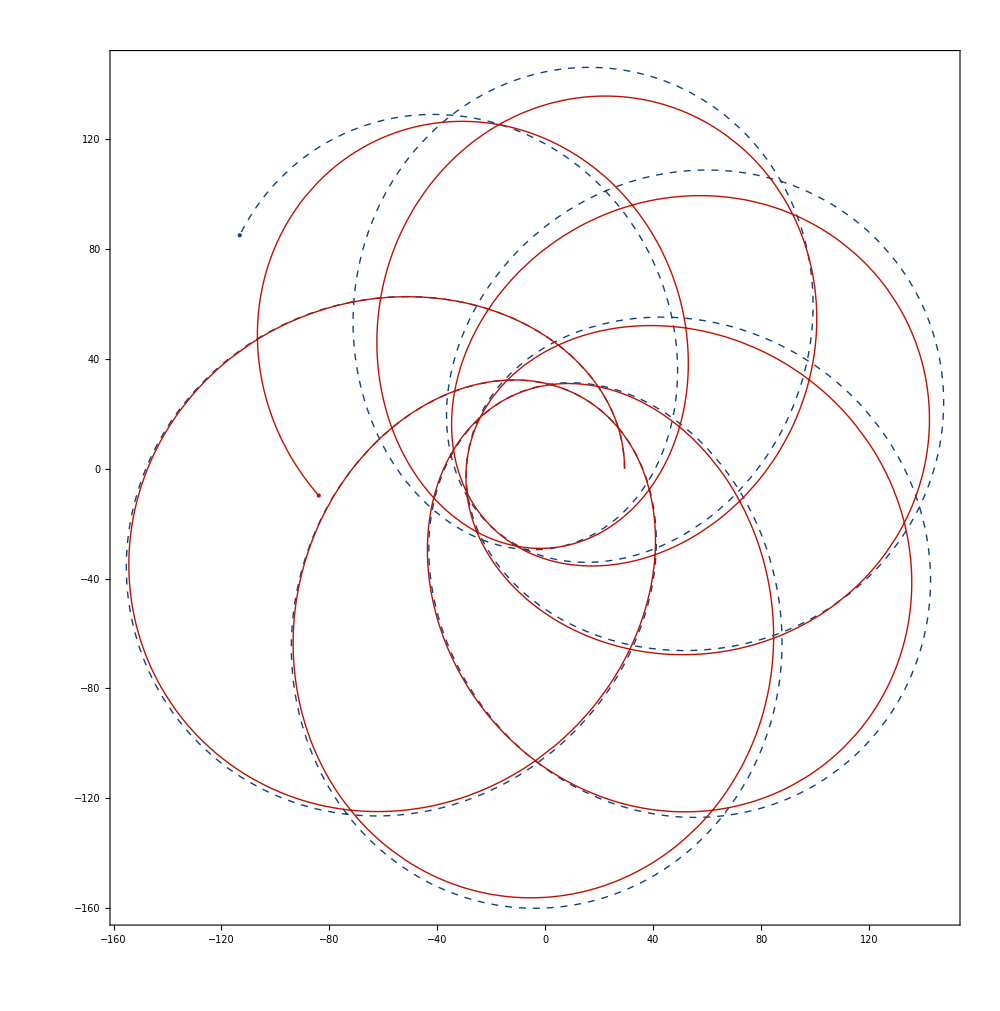

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,31000},Frame->True,ImageSize->1000,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->31000,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->31000}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->31000,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->31000}]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda=10^{-7}"]},{Left,Top}]]
```

```mathematica
Export["orbit_50_7_-7_v3.pdf",%]
```

orbit_50_7_-7_v3.pdf

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.4,p[0]==50,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-7],e'[t]==edot[p[t],e[t],10^-7],f'[t]==fdot[p[t],e[t],f[t],10^-7],δ'[t]==deldot[p[t],e[t],f[t],10^-7],f[0]==0,e[0]==0.4,p[0]==50,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

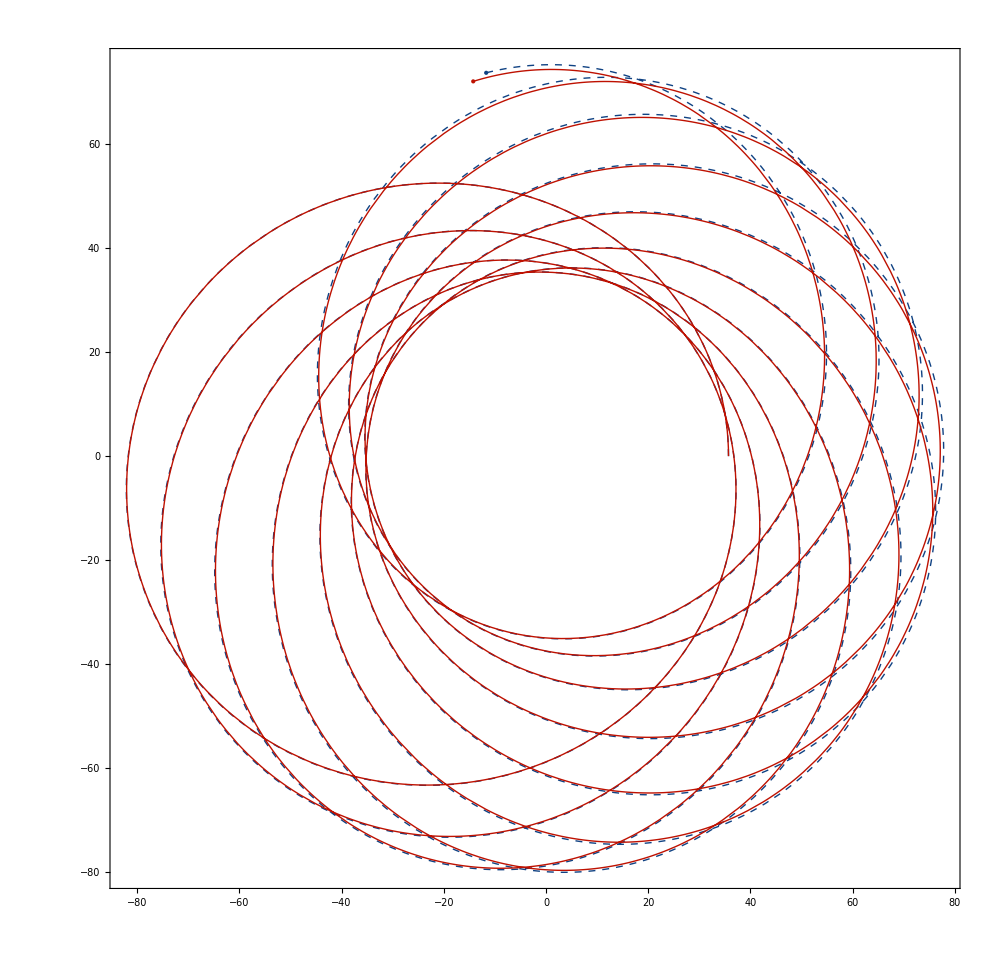

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,26000},Frame->True,ImageSize->1000,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->26000,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->26000}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->26000,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->26000}]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda=10^{-7}"]},{Left,Top}]]
```

```mathematica
Export["orbit_50_4_-7_v3.pdf",%]
```

orbit_50_4_-7_v3.pdf

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.7,p[0]==30,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-6],e'[t]==edot[p[t],e[t],10^-6],f'[t]==fdot[p[t],e[t],f[t],10^-6],δ'[t]==deldot[p[t],e[t],f[t],10^-6],f[0]==0,e[0]==0.7,p[0]==30,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

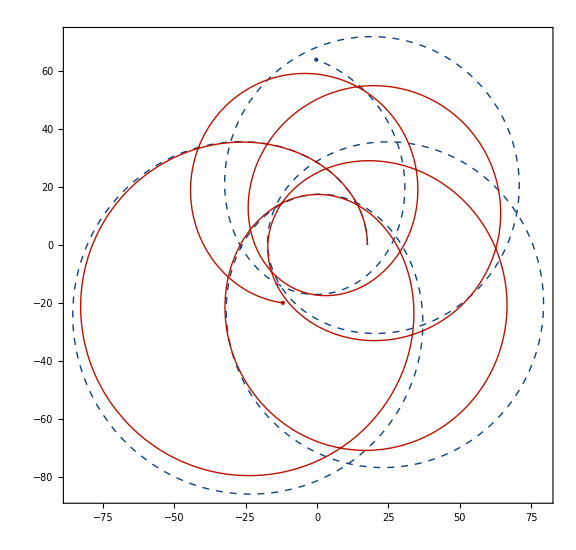

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,7700},Frame->True,ImageSize->Large,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->7700,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->7700}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->7700,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->7700}]}}]
```

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.4,p[0]==30,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-6],e'[t]==edot[p[t],e[t],10^-6],f'[t]==fdot[p[t],e[t],f[t],10^-6],δ'[t]==deldot[p[t],e[t],f[t],10^-6],f[0]==0,e[0]==0.4,p[0]==30,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

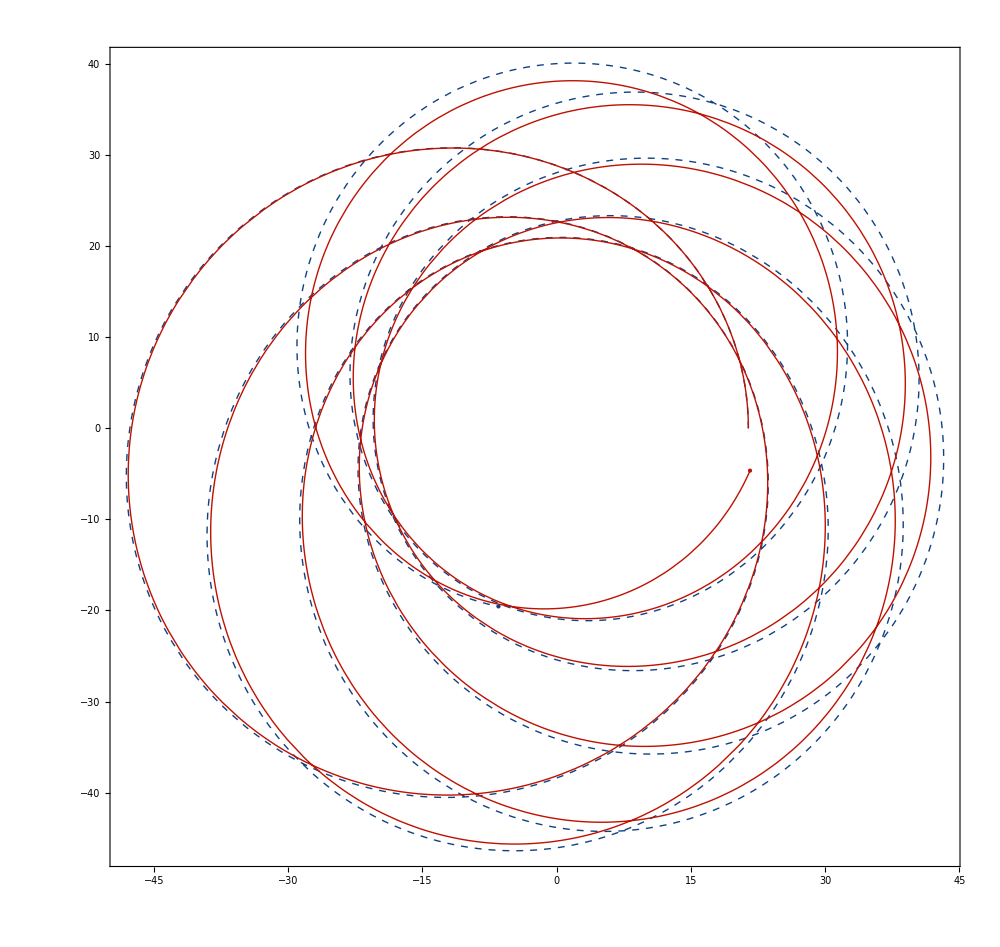

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,7000},Frame->True,ImageSize->1000,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->7000,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->7000}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->7000,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->7000}]}}]
```

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.7,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-8],e'[t]==edot[p[t],e[t],10^-8],f'[t]==fdot[p[t],e[t],f[t],10^-8],δ'[t]==deldot[p[t],e[t],f[t],10^-8],f[0]==0,e[0]==0.7,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

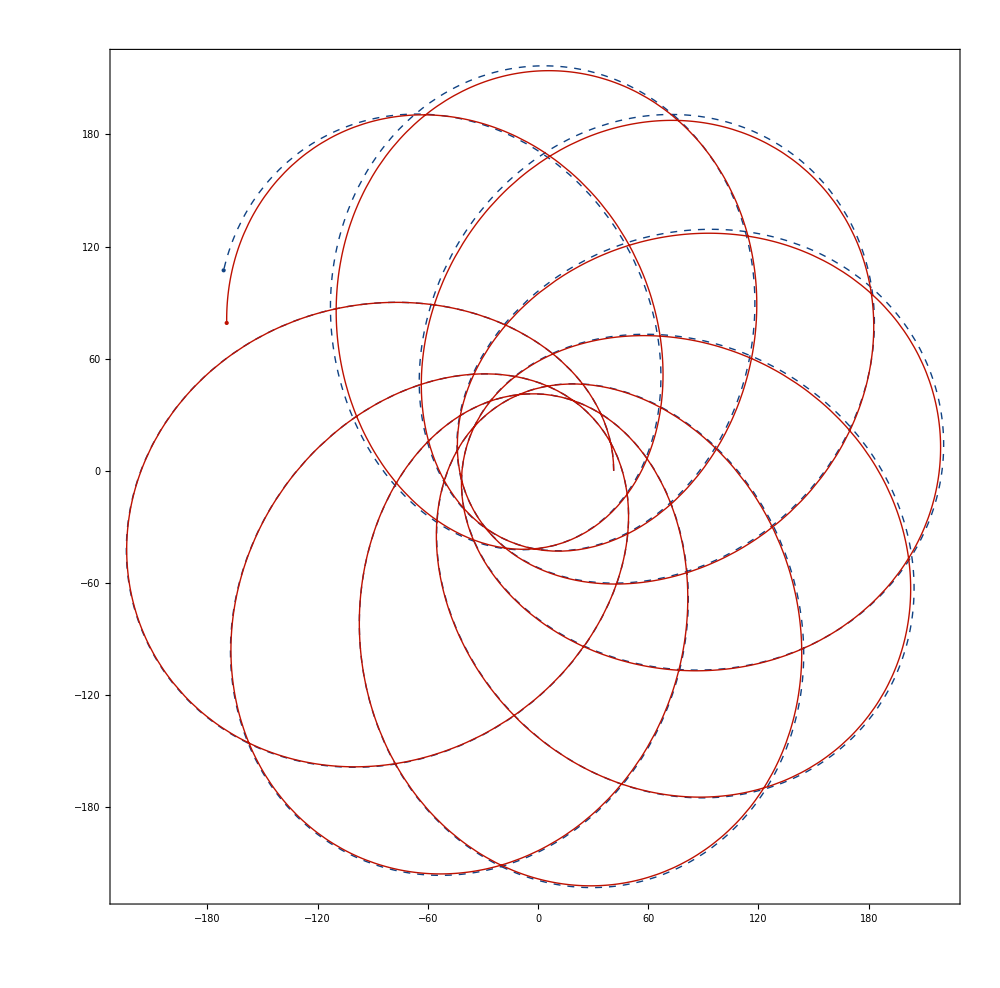

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,7.3*10^4},Frame->True,ImageSize->1000,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->7.3*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->7.3*10^4}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->7.3*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->7.3*10^4}]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda=10^{-8}"]},{Left,Top}]]
```

```mathematica
Export["orbit_70_7_-8.pdf",%]
```

orbit_70_7_-8.pdf

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.4,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-8],e'[t]==edot[p[t],e[t],10^-8],f'[t]==fdot[p[t],e[t],f[t],10^-8],δ'[t]==deldot[p[t],e[t],f[t],10^-8],f[0]==0,e[0]==0.4,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

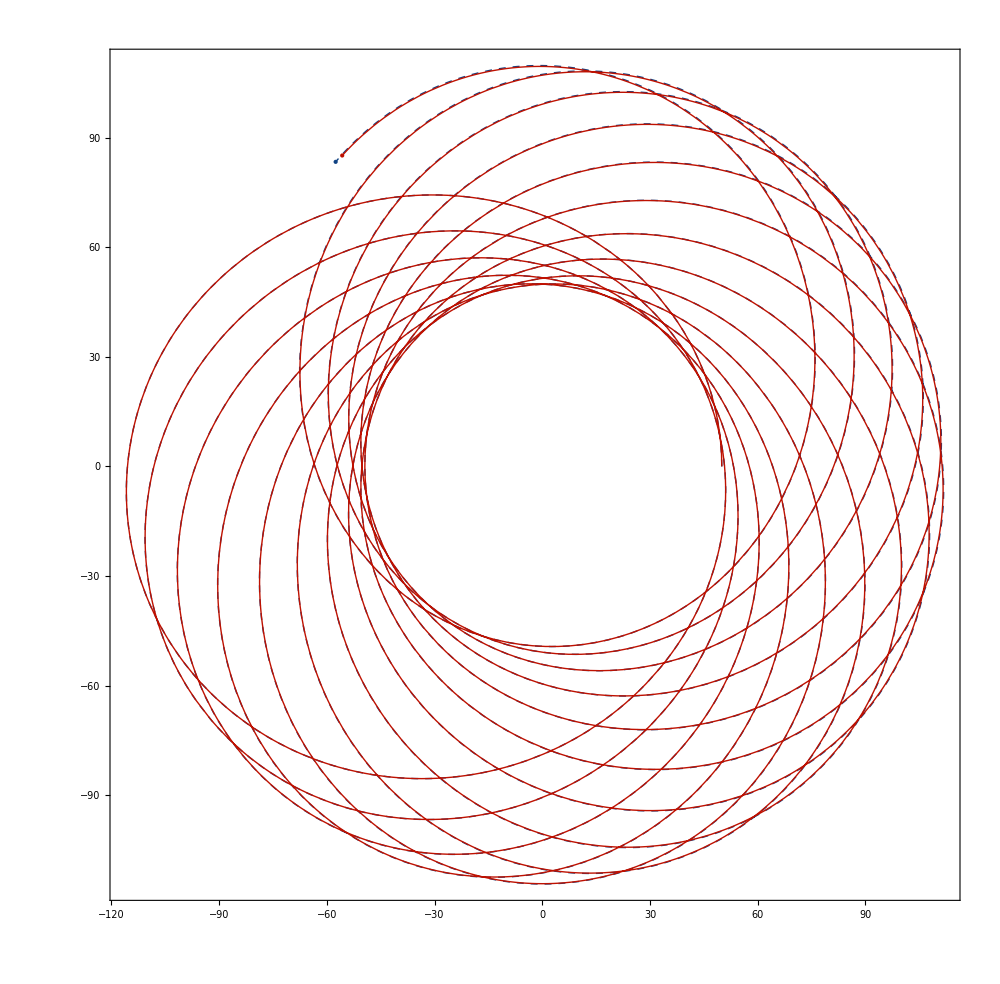

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,6.3*10^4},Frame->True,ImageSize->1000,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->6.3*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->6.3*10^4}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->6.3*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->6.3*10^4}]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda=10^{-8}"]},{Left,Top}]]
```

```mathematica
Export["orbit_70_4_-8.pdf",%]
```

orbit_70_4_-8.pdf

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.7,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-7],e'[t]==edot[p[t],e[t],10^-7],f'[t]==fdot[p[t],e[t],f[t],10^-7],δ'[t]==deldot[p[t],e[t],f[t],10^-7],f[0]==0,e[0]==0.7,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

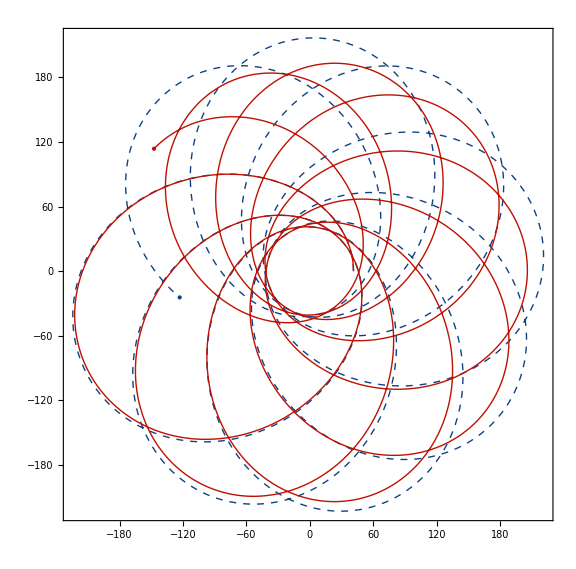

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,7.5*10^4},Frame->True,ImageSize->Large,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->7.5*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->7.5*10^4}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->7.5*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->7.5*10^4}]}}]
```

```mathematica
sol1=NDSolve[{p'[t]==pdot[p[t],e[t],0],e'[t]==edot[p[t],e[t],0],f'[t]==fdot[p[t],e[t],f[t],0],δ'[t]==deldot[p[t],e[t],f[t],0],f[0]==0,e[0]==0.4,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
sol2=NDSolve[{p'[t]==pdot[p[t],e[t],10^-6],e'[t]==edot[p[t],e[t],10^-6],f'[t]==fdot[p[t],e[t],f[t],10^-6],δ'[t]==deldot[p[t],e[t],f[t],10^-6],f[0]==0,e[0]==0.4,p[0]==70,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"]},{p,e,f,δ},{t,0,1000000}][[1]]
```

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

NDSolve::ndsz: At t == 233251., step size is effectively zero; singularity or stiff system suspected.

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],f→InterpolatingFunction[…],δ→InterpolatingFunction[…]}

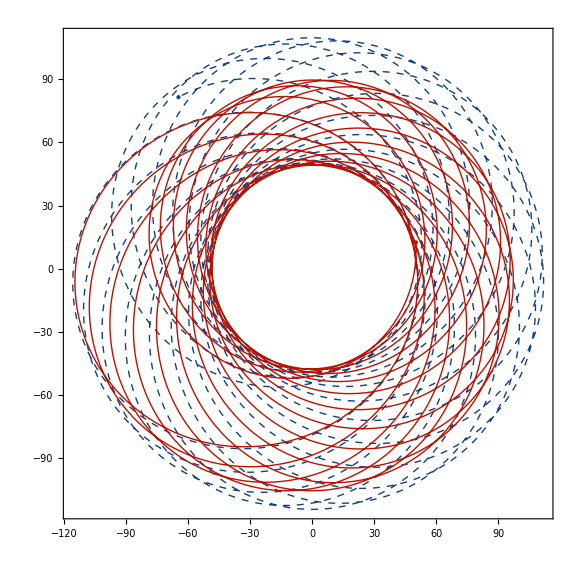

```mathematica
ParametricPlot[{{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1},{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2}},{t,0,7.5*10^4},Frame->True,ImageSize->Large,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol1/.t->7.5*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol1/.t->7.5*10^4}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]]/.sol2/.t->7.5*10^4,p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]]/.sol2/.t->7.5*10^4}]}}]
```